## An Abstract Model of Historical Processes - Code

## Context

This Mathematica notebook implements a sociological model of power struggles described in my (draft) paper “An Abstract Model of Historical Processes.”  For more information, please see the paper itself, which is also in the Github repository github.com/mpoulshock/AMHP.

Author: Michael Poulshock, Drexel University Thomas R. Kline School of Law, mp988@drexel.edu, mpoulshock@gmail.com.

## Implementation

### Data Structure Summary

#### Tactic matrix

An example of a tactic matrix (representing all of the agents’ tactic vectors), displayed in matrix form.  Each agent is allocating half of its power to itself, as indicated by the main diagonal.  Note that the absolute values of the cells in each column sum to one.

```mathematica
{{0.5,0.3},{-0.5,0.7}}// MatrixForm
```

(0.5 | 0.3
-0.5 | 0.7)

The tactic matrix is composed of each agent’s tactic vector:

```mathematica
Transpose[{{0.5,0.3},{-0.5,0.7}}][[1]]
```

{0.5,-0.5}

The absolute value of a tactic vector must always sum to one:

```mathematica
Total[Abs[%]]
```

1.

#### Game state

The game state is represented as an association that includes agent sizes, a tactic matrix, a utility vector, and a distance vector.

```mathematica
<|"sizes"->{4.3,4.2},"tactics"->{{0.5,0.5},{-0.5,0.5}},"util"->{2.2,2.1},"dx"->{0,0} |>
```

#### Options list

The options list is a data structure used to specify game parameters:

```mathematica
<|"n"-> 3,"α"-> 2.5, "β"-> 1.1, "μ"-> 3, "δ"-> 0.8, "ρ"-> 0.01,"breadth"-> 20,"depth"->3,"nearness" -> 0.1|>
```

Here are the meaning and ranges of these parameters (see the paper for details):

n | Number of players | ∈[1,∞) | Int
α | Utility exponent | ∈[2,3] | Real
β | Benevolence multiplier | ∈(0,μ) | Real
μ | Malevolence multiplier | ∈(β,∞) | Real
δ | Discounting factor | ∈(0,1) | Real
ρ | Coefficient of inertia | ∈(0,n] | Real
breadth | Tactics per player | ∈[1,∞) | Int
depth | Depth of simulation | ∈[1,∞) | Int
nearness | Tactical variation in simulation | ∈(0,1] | Real

#### Reel

A reel is a list of game states that can be played frame-by-frame to illustrate the evolution of a system of interacting, power-seeking agents.

```mathematica
{state0, state1, ...}
```

### Game State

#### Nearby tactics

Given a random vector, this function adjusts its length so as to make it a legal tactic.  A legal tactic is a point on the surface of a cross-polytope whose dimension is equal to the number of agents.  The visualization below illustrates this shape for a population of three agents.  We assume that agents do not harm themselves.

```mathematica
normalize[vector_] := N[vector / Total[Abs[vector]]]
```

Try using Round to improve performance?

```mathematica
normalize[vector_] :=Round[vector / Total[Abs[vector]],0.001]
```

```mathematica
normalize[{3,22,1,-4}]
```

{0.1,0.7333,0.0333,-0.1333}

Finds tactics “near” a given tactic.  Method: Add random variates to each element of the input tactic, then normalize the vector so it is on the surface of the cross polytope.  If the vector contains negative tactic for a given agent (indicating self-harm), ignore the result and look for a new nearby random tactic.

```mathematica
randomTacticNear[point_, agentIndex_, ρ_] := Block[{newRaw},
newRaw = point + RandomVariate[NormalDistribution[0,ρ],Length[point]];
If[newRaw[[agentIndex]] < 0, Return[randomTacticNear[point, agentIndex, ρ]]];
Return[normalize[newRaw]];
]
```

Same as above, but it generates a list of nearby tactics:

```mathematica
randomTacticNear[point_, a_, ρ_,numberOfTactics_] := Table[randomTacticNear[point, a, ρ],numberOfTactics]
```

```mathematica
randomTacticNear[{1,0,0}, 1,5 ]
```

{0.254015,0.258943,0.487042}

```mathematica
randomTacticNear[{1,0,0}, 1,5,5 ] // Column
```

{0.0773758,0.471254,-0.45137}
{0.713559,0.119472,-0.166969}
{0.330579,0.455018,-0.214403}
{0.603187,0.138673,0.258141}
{0.560809,0.307408,-0.131782}

A cross-polytope in dimension 3 is an octahedron, shown below.  Legal tactics are points on the surface of this shape.  The widget below starts from a given point (pt) and then generates random points nearby, where the slider controls the degree of nearness.

```mathematica
Manipulate[
pt = {0.7,0.1,0.2};
Show[{
Graphics3D[Scale[PolyhedronData["Octahedron","Faces"],1.4,{0,0,0}]],
Graphics3D[{PointSize[0.02],Point[pt]}],
Graphics3D[Point[randomTacticNear[pt,3,nearness,100] ], PlotRange->{{-1,1},{-1,1},{-1,1}}]
}],{nearness,0.0001,1}]
```

#### Nearby matrices

This function takes a tactic matrix and returns a random “nearby” matrix in which every agent’s tactic is near their old one.

```mathematica
randomMatrixNear[startingMatrix_, ρ_] := Transpose[Table[randomTacticNear[startingMatrix[[All,a]], a,ρ],{a,1,Length[startingMatrix]}]]
```

```mathematica
randomMatrixNear[{{0.841,0.343},{0.158,0.656}},0.01]
```

{{0.839462,0.35115},{0.160538,0.64885}}

For each agent, generate a list of random tactics.  Then, given those tactics, generate an ensemble of random tactic matrices, representing all combinations of all agents’ tactics.  The total number of matrices created is noOfTactics^noOfAgents.  For performance reasons, this function does not use randomMatrixNear.

```mathematica
matrixPermutations[startingMatrix_, noOfTacticsPerAgent_, ρ_] := Map[Transpose,Tuples[Table[randomTacticNear[startingMatrix[[All,a]], a,ρ,noOfTacticsPerAgent],{a,1,Length[startingMatrix]}]]]
```

```mathematica
matrixPermutations[{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}},50,0.05]; // AbsoluteTiming
```

{0.037062,Null}

#### New game state

Creates a new game state object:

```mathematica
newState[sizes_,tactics_,options_]:= 
 <|"sizes"->sizes,
"tactics"->tactics,
"util"->utility[sizes,options["α"]],
"dx"->Table[0,options["n"]] |>
```

```mathematica
newState[{1,1,1},{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}},<|"α"-> 2.5, "n"->3|>]
```

<|sizes→{1,1,1},tactics→{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}},util→{0.333333,0.333333,0.333333},dx→{0,0,0}|>

#### Random game states

Creates a random tactic matrix at a specified degree of nearness from the identity matrix (in which every agent is allocation 100% of its power to itself).  n is the number of agents.

```mathematica
randomTacticMatrix[n_, ρ_] := randomMatrixNear[IdentityMatrix[n], ρ]
```

```mathematica
randomTacticMatrix[3,0.1] // MatrixForm
```

(0.97525 | 0.0414935 | 0.0746378
0.00872482 | 0.726465 | -0.0511621
-0.0160252 | -0.232042 | 0.8742)

Generate a random initial game state, specifying the number of nodes (n), the maximum node size, and the degree of nearness from the identity matrix:

```mathematica
randomGameState[options_] := Block[{n=options["n"]},
newState[RandomReal[{0,options["maxInitSize"]},n],randomTacticMatrix[n,options["ρ"]],options]
]
```

```mathematica
randomGameState[<|"n"->3,"α"-> 2.5,"ρ"->0.1,"maxInitSize"->1|>]
```

<|stateID→43129724229,sizes→{0.23227,0.831757,0.0966389},tactics→{{0.905345,-0.169597,0.0242527},{-0.0271939,0.794843,0.0249468},{0.0674612,0.0355596,0.9508}},path→{43129724229},util→{0.0344327,0.835569,0.00384478},dx→{0,0,0}|>

```mathematica
showStateGrid[randomGameState[<|"n"->3,"α"-> 2.5,"ρ"->0.1,"maxInitSize"->1|>]]
```

1 | 2 | 3
0.808 | 0.011 | 0.137
0.88 | -0.05 | -0.01
0.07 | 0.92 | -0.08
0.05 | -0.04 | 0.91

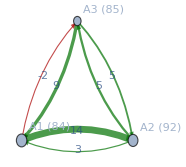

```mathematica
displayGraph[randomGameState[<|"n"->3,"α"-> 2.5,"ρ"->0.1,"maxInitSize"->1|>],True]
```

#### Update game state

At every time step, we update the state of the nodes (which may grow or shrink) to get a new game state.  Procedure used: (1) multiply the tactics by the benevolence and malevolence constants, (2) use matrix multiplication to obtain the new node sizes.

```mathematica
updateState[parentState_,newTactics_,options_] :=updateState[parentState,newTactics,{options["n"],options["β"],options["μ"],options["α"],options["δ"]}]
```

```mathematica
updateState[parentState_,newTactics_,{n_,β_,μ_,α_,δ_}]:= Block[{skewedTactics,newNodes,newUtil,dx},

(* Apply the benevolence & malevolence constants to the tactic matrix *)
skewedTactics = tacticSkew[newTactics,n,μ,β]; 

(* Use the dot product to get the new node sizes. Ensure that the result does not produce nodes with negative sizes. *)
newNodes = Map[Max[#,0]&, Dot[skewedTactics,parentState["sizes"]]];

(* Calculate the "tactical distance" from the parent tactic matrix to the child matrix. *)
dx = tacticalDistance[parentState["tactics"],newTactics];

newUtil =utility[newNodes,α];

Return[<|
"sizes" ->newNodes,
"tactics" -> newTactics,
"util"->newUtil,
"dx"->dx
|>]
]
```

Some tests of the function above:

```mathematica
randomGameState[<|"n"->3,"α"-> 2.5,"ρ"->0.1,"maxInitSize"->1|>]
```

<|sizes→{0.411065,0.147745,0.06501},tactics→{{0.880488,-0.0268662,-0.00195115},{0.031646,0.942066,-0.0576269},{-0.0878662,-0.031068,0.940422}},util→{0.55549,0.0430212,0.00552523},dx→{0,0,0}|>

```mathematica
updateState[%,randomTacticMatrix[3,0.1],{2,1.1,3,2.5,0.8}]
```

<|sizes→{0.35096,0.170237,0.0961893},tactics→{{0.871885,0.0432956,-0.0742345},{0.0767573,0.89269,0.0508914},{0.051358,0.064014,0.874874}},util→{0.452089,0.0740829,0.0177786},dx→0.243293|>

Before doing the matrix multiplication, we multiply the cells in the tactic matrix by either a conflict factor (if the tactic is negative) or a cooperation factor (if it’s positive).  Any transfers of power from a node back to itself are not subject to this multiplication.

```mathematica
tacticSkew[tactics_,n_,μ_,β_] := Block[{newTactics},

(* Increase all transfers to other nodes by the appropriate factor *)
 newTactics = Map[applySkew[#,μ,β]&,tactics, {2}];

(* Undo the increases for self-transfers (along the matrix diagonal) *)
For[i=1,i≤n,i++,  
newTactics[[i,i]] = tactics[[i,i]];
]; 

Return[newTactics];
];
```

```mathematica
applySkew=Compile[{{val,_Real},{conflict, _Real},{coop, _Real}},If[val<0, val*conflict, val*coop]]
```

CompiledFunction[…]

```mathematica
tacticSkew[{{1,1},{{0.8,0.3},{-0.2,0.7}}},3,2] // AbsoluteTiming
```

{3.21938×10^-6,tacticSkew[{{1,1},{{0.8,0.3},{-0.2,0.7}}},3,2]}

### Utility / Payoff

#### Utility function

This function determines the “utility” of an agent’s game position.  See the paper for more information.

```mathematica
utility[s_List,α_] := If[Total[s] == 0,s,s^α / Total[s^2]]
```

Might consider rounding for performance purposes:

```mathematica
utility[s_List,α_] := If[Total[s] == 0,s,Round[s^α / Total[s^2],0.0001]]
```

```mathematica
utility[{1,2,3,4},2.5]
```

{0.0333,0.1886,0.5196,1.0667}

```mathematica
utility[{0,0},2.5]
```

{0,0}

#### Tactical distance

Determine the “distance” between two tactic vectors.

```mathematica
tacticalDistance[a_,b_] := Norm[Map[EuclideanDistance[#[[1]],#[[2]]]&,Transpose[{Transpose[a],Transpose[b]}]]]
```

```mathematica
a={{0.964,0.038,0.022},{0.008,0.896,0.012},{0.028,-0.067,0.966}};
```

```mathematica
b ={{0.846,0.164,0.036},{-0.103,0.719,0.123},{0.051,-0.117,0.841}};
```

```mathematica
{a//MatrixForm,b//MatrixForm}
```

{(0.964 | 0.038 | 0.022
0.008 | 0.896 | 0.012
0.028 | -0.067 | 0.966),(0.846 | 0.164 | 0.036
-0.103 | 0.719 | 0.123
0.051 | -0.117 | 0.841)}

```mathematica
tacticalDistance[a,b]
```

0.323452

```mathematica
Clear[a]; Clear[b];
```

```mathematica
tacticalDistance[{{1.,-0.39},{0,0.61}},{{1.,-0.3},{0,0.7}}]
```

0.127279

```mathematica
Norm
```

#### Payoff

The payoff is the utility of a position multiplied by the likelihood of reaching it.

```mathematica
payoff[utility_, dx_,options_] :=utility*dxProbability[dx,options["σ"]]
```

Determines the likelihood that a tactical shift of a given distance will be achieved.

```mathematica
dxProbability[dx_,σ_] := N[PDF[NormalDistribution[0,σ],dx]]
```

```mathematica
dxProbability[0.6,1]
```

0.333225

```mathematica
Manipulate[Plot[dxProbability[x,σ] ,{x,0,10},PlotRange->{{0,5},{0,2}}],{{σ,1},0.00001,5}]
```

```mathematica
PDF[NormalDistribution[0,σ],x]// TraditionalForm
```

(ⅇ^(-x^2/(2 σ^2)))/(√(2 π) σ)

#### Intertemporal Utility

Get the intertemporal utility vector for the players’ strategies on a particular game path.

```mathematica
intertemporalUtility[gamePath_,options_]:=Block[{expectedUtilityOverTime,deltaVec},

(* Utility * dxProbability at each game state on the path, for each player *)
expectedUtilityOverTime= Transpose[Map[payoff[#util,#dx,options]&,gamePath]];

(* Not that efficient, but using Length[] ensures that the δ-vector is always the correct size. *)
deltaVec = deltaVector[options["δ"],Length[expectedUtilityOverTime[[1]]]-1 ];

(* Calculate intertemporal utility for each player. Use Rest[] to ignore the origin state. *)
(1-options["δ"])* Map[Total[Rest[#]* deltaVec] &,expectedUtilityOverTime]
]
```

```mathematica
intertemporalUtility[%145,<|"σ"->0.5,"δ"-> 0.8|>]
```

{0.470501,0.115578,0.360854}

Create a list of the intertemporal discount factor at all relevant time periods, e.g. {1, 0.70, 0.49, 0.34, 0.24...}.  The first value is always 1, to reflect the fact that a player is guaranteed to get the full amount of the utility of their next move (there is no discounting or uncertainty).  The vector is cached so it doesn’t have to be recomputed every time.

```mathematica
deltaVector[δ_,depth_] := deltaVector[δ,depth] = Table[δ^i,{i,0,depth-1}];
```

```mathematica
deltaVector[0.8,3]
```

{1.,0.8,0.64}

```mathematica
Clear[deltaVector]
```

#### Individual rationality

This function helps determine whether an intertemporal utility vector (representing the IU of all players) is preferable to another path in which all game states (except the first) are Nash equilibria.  Determines whether every element in list1 is greater than the corresponding element in list2.

```mathematica
listDominatesQ[list1_, list2_] :=ContainsOnly[Map[#> 0&,list1-list2],{True}]
```

```mathematica
listDominatesQ[{0.2,9,3.01},{1,2,3}]
```

False

We are only interested in IU vectors in which every element is greater than the corresponding element of all stage NE vectors.  This function gets the maximum value for each position in the vector.  A path’s IU vector only needs to be larger than this (that is, every element of the IU vector has to be larger than the corresponding element of the threshold vector).

```mathematica
iuThresholdVector[vectors_List] :=  Map[Max[#]&,Transpose[vectors]]
```

```mathematica
iuThresholdVector[{{2,1,3},{3,5,0},{1,1,2}}]
```

{3,5,3}

### Game Tree

#### Generate strategies

Starting from a given tactic, this function generates a series of nearby tactics (a “strategy”).  Each tactic is near the prior one.

```mathematica
generateStrategy[tactic_,agentIndex_,depth_,nearness_] := Rest[Nest[Append[#,randomTacticNear[Last[#], agentIndex, nearness] ]&,{tactic},depth]]
```

```mathematica
generateStrategy[{1,0,0},3,4,0.1] // Column
```

{0.910677,0.0675258,0.0217968}
{0.900564,-0.0372407,0.0621954}
{0.907832,0.0721304,0.0200376}
{0.744942,0.127803,0.127255}

Generate multiple strategies for a player:

```mathematica
generateStrategies[tactic_,agentIndex_,depth_,nearness_,noOfStrategies_] := Table[generateStrategy[tactic,agentIndex,depth,nearness],noOfStrategies]
```

```mathematica
generateStrategies[{1,0,0},3,3,0.001,5]
```

{{{0.999224,0.000766702,8.93033×10^-6},{0.998729,0.000447345,0.000824043},{0.997027,0.00143716,0.00153557}},{{0.995999,-0.00209673,0.00190381},{0.994122,-0.00304006,0.00283759},{0.995119,-0.00253413,0.00234652}},{{0.999382,-0.000439519,0.000178405},{0.997764,-0.0014135,0.000822771},{0.997439,-0.00148402,0.00107696}},{{0.998372,0.000889242,0.000739135},{0.999479,0.000303898,0.000216892},{0.997923,-0.00128109,0.000795813}},{{0.999526,0.000441647,0.0000319988},{0.998255,-0.000607442,0.00113751},{0.997254,-0.00113606,0.00161021}}}

Generate a list of strategies for each player:

```mathematica
generateAllStrategies[tacticMatrix_,options_] := Array[generateStrategies[tacticMatrix[[All,#]],#,options["depth"],options["nearness"],options["breadth"]]&,options["n"]]
```

```mathematica
generateAllStrategies[IdentityMatrix[3],<|"n"-> 3,"depth"-> 3,"breadth"->4,"nearness"-> 0.05|>] // Column
```

{{{0.92742,0.0402191,0.032361},{0.896684,0.0520403,-0.0512761},{0.817226,0.0888187,-0.0939556}},{{0.965331,0.0242337,0.010435},{0.929747,0.0694248,0.000828525},{0.968687,-0.00405576,0.0272576}},{{0.878234,-0.0656131,-0.0561526},{0.85728,-0.11006,-0.0326604},{0.883227,-0.0247836,-0.0919895}},{{0.925743,-0.00402551,-0.0702311},{0.873014,0.0202362,-0.10675},{0.904423,-0.0346232,-0.0609534}}}
{{{-0.0618338,0.900061,0.0381054},{-0.0708897,0.905264,0.0238468},{-0.0843828,0.865025,0.0505917}},{{-0.0599652,0.928016,-0.0120184},{0.0340046,0.917928,-0.0480672},{0.084089,0.912132,-0.00377931}},{{-0.0902882,0.891946,-0.0177661},{-0.0598819,0.900179,-0.039939},{-0.0114966,0.916759,-0.0717442}},{{-0.0229299,0.943458,-0.0336122},{-0.0174433,0.950682,-0.031875},{-0.0848273,0.877055,-0.0381177}}}
{{{0.00677539,-0.0810989,0.912126},{0.00939878,-0.0822573,0.908344},{0.0132114,-0.0436091,0.943179}},{{-0.0210509,0.0639497,0.914999},{-0.0493701,-0.0194459,0.931184},{-0.00949153,-0.0572693,0.933239}},{{0.0343666,-0.0129083,0.952725},{-0.0483556,-0.00394695,0.947697},{-0.0912776,0.0267647,0.881958}},{{0.0538701,0.0120266,0.934103},{0.0544217,0.033293,0.912285},{0.0486777,0.0330123,0.91831}}}

#### Play out a game thread

Given a strategy for each player, play out the sequence of moves and determine the results at each step.

```mathematica
playGameThread[initialState_,strategies_List,options_] := FoldList[updateState[#1,Transpose[#2],options]&,initialState,Transpose[strategies]]
```

```mathematica
state=newState[{1,1,1},{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}},<|"α"-> 2.5,"n"->3|>]
```

<|stateID→809075705124,sizes→{1,1,1},tactics→{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}},path→{809075705124},util→{0.333333,0.333333,0.333333},dx→{0,0,0}|>

```mathematica
list = {{{1,0,0},{0.9510380075162788,-0.018757158917374228,-0.03020483356634686}},{{0,1,0},{-0.15118214271476668,0.7520810590608245,-0.09673679822440885}},{{0,0,1},{-0.13514701485485778,-0.027572101428419128,0.8372808837167232}}};
```

```mathematica
playGameThread[state,list,{3,1.1,2,2.5,0.6}]
```

{<|stateID→809075705124,sizes→{1,1,1},tactics→{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}},path→{809075705124},util→{0.333333,0.333333,0.333333},dx→{0,0,0}|>,<|stateID→464224130862,sizes→{1.,1.,1.},tactics→{{1,0,0},{0,1,0},{0,0,1}},path→{809075705124,464224130862},util→{0.333333,0.333333,0.333333},dx→{0.707107,0.707107,0.141421}|>,<|stateID→948625654004,sizes→{0.853114,0.256243,0.511843},tactics→{{0.951038,-0.0187572,-0.0302048},{-0.151182,0.752081,-0.0967368},{-0.135147,-0.0275721,0.837281}},path→{809075705124,464224130862,948625654004},util→{0.636915,0.0314916,0.177584},dx→{0.20861,0.250152,0.191697}|>}

### Nash Equilibria

#### Explanation

This section explains the implementation of the algorithm that identifies Nash equilibria among the players’ strategies.  This algorithm is complex and probably counterintuitive because it makes implicit assumptions about one of its underlying data structures, and because it’s written in a functional rather than imperative style.  However, both of these aspects make it decently performant: the data structure avoids having to make an exponential number of lookups and comparisons, and the functional style makes the algorithm parallelizable.  Here’s how it works.

Each player has a certain number of strategies, a number we’ll call breadth.  Collectively, all players’ strategies are stored in a data structure like this (here n=2, breadth=3):
 strategies = 
  {{p1s1,
    p1s2,
    p1s3},
   {p2s1,
    p2s2,
    p2s3}}
This data structure allows strategies to be accessed by Part, for example strategies[[2,3]] will retrieve player 2’s third strategy.

We want to know every combination of all players’ strategies, so we can play out all possible games.  For example, if player one has strategies {1,2} and player two has strategies {1,2}, we want to see the outcomes of all games - that is, those with the strategy combinations {{1,1},{1,2},{2,1},{2,2}}.  These combinations are easily generated using Tuples.  (Note that even though both players have strategies with the id of 1, that doesn’t mean that they’re the same strategy.)

```mathematica
combos = Tuples[Range[2],3];
```

```mathematica
combos // Column
```

{1,1,1}
{1,1,2}
{1,2,1}
{1,2,2}
{2,1,1}
{2,1,2}
{2,2,1}
{2,2,2}

Each row in the above table represents a possible game and it shows which strategies each player chooses.  In the first row, each player plays their strategy that has the id of 1, and so on.  Through some procedures and manipulations described in the other sections of this document, we can end up with a data structure that has the same shape as the above table, but that contains the intertemporal utility (IU) payoff values of each game.  Here’s an example (populated with random numbers):

```mathematica
Round[RandomReal[{0,1},{8,3}],0.01] // Column
```

{0.41,0.32,0.04}
{0.28,0.86,0.01}
{0.28,0.63,0.44}
{0.68,0.14,0.55}
{0.59,0.15,0.78}
{0.51,0.46,0.95}
{0.18,0.42,0.23}
{0.22,0.1,0.03}

Each row in this IU table corresponds to the same row in the strategy combination table.  (This is the assumption that we’re making and that we have to ensure that the code respects.)

A Nash equilibrium is a game outcome in which no player could do better by changing their strategy.  In other words, it’s an outcome in which every player plays the best response to every other player’s possible strategies.  In this game, there are typically multiple equilibria, but sometimes one and, rarely, none.

In a two player game, outcomes can be organized in a 2 x breadth payoff matrix.  A three player game would have a payoff cube and an n-player game would have a payoff hypercube.  The IU table above is a serialized representation of every cell in a payoff matrix/cube/hypercube: it’s a list rather than an n-dimensional data structure.  There are breadth^n rows in this table.

We can exploit the numeric pattern in the combos table to quickly identify a player’s best move for a given situation.  For example, look at the first two rows of the combos table:

{1,1,1}
{1,1,2}

This snippet shows all the games where players one and two play strategy 1, along with player three’s two responses.  We can find player three’s best response by identifying the rows with the maximum IU values in the corresponding cells in the IU table.  If we then “slide down” column three of the IU table, making similar comparisons as we go, we can identify all of player three’s best responses for the various other situations that she might encounter.  We can do the same for players one and two, but with different patterns of sliding down: the spacing and grouping of “comparable” cells will be different in each column.  

{1,1,1}
{1,1,2}
{1,2,1}
{1,2,2}
{2,1,1}
{2,1,2}
{2,2,1}
{2,2,2}        {1,1,1}
{1,1,2}
{1,2,1}
{1,2,2}
{2,1,1}
{2,1,2}
{2,2,1}
{2,2,2}        {1,1,1}
{1,1,2}
{1,2,1}
{1,2,2}
{2,1,1}
{2,1,2}
{2,2,1}
{2,2,2}

The algorithm below implements this idea in bestResponsesForPlayer, altering the way is slides and groups comparable cells, based on n, breadth, and the player number.  The nashEquilibria function collates the best responses for each column (player) and then uses Intersection to find the rows (strategy combos) in which every player has a best response.

#### Implementation

Identify strategy combinations that are Nash equilbria:

```mathematica
nashEquilibria[utilTable_, options_] := Block[{bestResponsesByPlayer,nashIDs, n=options["n"]},

(* Find each player's best responses *)
bestResponsesByPlayer = ParallelArray[bestResponsesForPlayer[utilTable[[All,#]],options["breadth"],n,#] &,n];

(* Rows that are Nash equilibria *)
nashIDs = Apply[Intersection,bestResponsesByPlayer];

Return[nashIDs];
]
```

This is the most complicated function in the implementation.  See the explanation above for context.  This function identifies the best responses for each player, given the various strategies of other players:

```mathematica
bestResponsesForPlayer[utils_List,breadth_,n_,player_] := Block[{col,indexedUtils,segments,comparables,subsegments},

(* Reverse the index number of the column *)
(* e.g. instead of {1,2,3,4} use column numbers {4,3,2,1} *)
col=n-player + 1;

(* Match each utility value with an index number, to keep track of the corresponding row *)
(* e.g. convert utility values {a,b,c} into {{1,a},{2,b},{3,c}} *)
indexedUtils =Partition[Riffle[Range[Length[utils]],utils],2];

(* Break the column up into segments based on the breadth and (reversed) column index *)
segments = Partition[indexedUtils,breadth^col];

(* The rightmost column doesn't need to be subsegmented, since comparable cells are always adjacent.  Otherwise... *)
If[col==1,comparables=segments,

(* Break each segment down further to "line up" comparable cells *)
subsegments =Map[Partition[#,breadth^(col-1)]&,segments];

(* Group utility values that should be compared with each other *)
(* Flatten to remove redundant {}'s that have built up *)
comparables = Flatten[Map[Transpose,subsegments],1]
];

(* Find the best responses within each group of comparables, then Flatten the results into a single list *)
Return[Flatten[Map[maxIDs,comparables]]];
]
```

Tests:

```mathematica
test=RandomInteger[10,3^3]
```

{6,2,1,5,4,4,1,0,3,0,1,9,10,4,0,1,8,0,7,4,10,9,9,3,10,5,0}

```mathematica
Partition[test,9] // MatrixForm
```

(6 | 2 | 1 | 5 | 4 | 4 | 1 | 0 | 3
0 | 1 | 9 | 10 | 4 | 0 | 1 | 8 | 0
7 | 4 | 10 | 9 | 9 | 3 | 10 | 5 | 0)

```mathematica
bestResponsesForPlayer[test,3,3,3]
```

{1,4,9,12,13,17,21,22,23,25}

```mathematica
bestResponsesForPlayer[test,3,3,2]
```

{1,5,6,13,17,12,25,23,21}

```mathematica
bestResponsesForPlayer[test,3,3,1]
```

{19,20,21,13,23,6,25,17,9}

Given {id, value} pairs, return the ids of the maximum values:

```mathematica
maxIDs[list_]:=Map[First,MaximalBy[list,Last]]
```

```mathematica
maxIDs[{{1,7},{2,7},{3,3}}]
```

{1,2}

### Simulations

#### Frame

Run one frame of the simulation.  Assuming that ParallelMap returns results in same order as Map (as WL documentation suggests); if incorrect,outcomes may no longer correspond to the strategy combo ids.

```mathematica
runFrame[initialState_, options_] := Block[{strategies,combos,iuData, iuDataTransposed,stageGameNashRows,minimax,repeatedGameNashRowIDs,nashThreads},

(* Generate strategies for each player *)
strategies = generateAllStrategies[initialState["tactics"],options];

(* Generate ids to go with the various strategy combos *)
combos = Tuples[Range[options["breadth"]],options["n"]];

(* For each combo, play out all moves on the game tree path *)
(* To save space, keep only the resulting IU vector instead of the each game thread (which is a list of game states) *)
iuData = ParallelMap[
stageAndIntertemporalPayoffs[
playGameThread[initialState,getStrategiesByID[strategies,#],options]
,options]
&,combos];

(* Transpose it in order to pick out the stage from the repeated game payoffs *)
iuDataTransposed = Transpose[iuData];

(* Find the Nash equilibria of the stage game *)
stageGameNashRows=nashEquilibria[iuDataTransposed[[1]],options];

(* Get the stage payoffs of all NEs, then find the "minimax" threshold *)
minimax = iuThresholdVector[Map[payoff[#[[2,"util"]],#[[2,"dx"]],options]&,getGameThreads[initialState, strategies, combos, stageGameNashRows, options]]];

(* Find all game threads that are NEs of the repeated game by iterating through list of IUs *)
repeatedGameNashRowIDs = MapIndexed[If[listDominatesQ[#1, minimax],First[#2],Nothing] &,iuDataTransposed[[2]]];

(* Return the game threads for the repeated game NEs *)
nashThreads = getGameThreads[initialState, strategies, combos, If[Length[repeatedGameNashRowIDs]==0,stageGameNashRows,repeatedGameNashRowIDs], options];

Return[nashThreads];
]
```

Returns the payoff of the stage game as well as the intertemporal payoffs, as {stagePayoffList, intertemporalPayoffList}.

```mathematica
stageAndIntertemporalPayoffs[gamePath_,options_] := {
payoff[gamePath[[2,"util"]],gamePath[[2,"dx"]],options],
intertemporalUtility[gamePath,options]
}
```

```mathematica
state=newState[{1,1,1},{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}},<|"α"-> 2.5,"n"->3|>];
```

```mathematica
runFrame[state,<|"n"-> 3,"α"-> 2.9, "β"-> 3.1, "μ"-> 5, "δ"-> 0.9, "σ"-> 1,"breadth"->4,"depth"->20,"nearness" -> 0.05|>]
```

Given a list of row numbers, play the game thread for each row.

```mathematica
getGameThreads[initialState_, strategies_, combos_, gameRows_, options_] := Map[playGameThread[initialState,getStrategiesByID[strategies,combos[[#]]],options]&,gameRows]
```

Given a list of all strategies for all players and a list of strategy IDs, this returns a list of the corresponding strategies.

```mathematica
getStrategiesByID[strategyDB_,ids_List] := MapIndexed[strategyDB[[#2[[1]],#1]]&,ids];
```

```mathematica
test = generateAllStrategies[IdentityMatrix[3],<|"n"-> 3,"depth"-> 3,"breadth"->4,"nearness"-> 0.3|>]
```

{{{{1,0,0},{0.710002,0.0607152,0.229283},{0.652199,-0.256713,-0.0910873},{0.441931,-0.328475,-0.229594}},{{1,0,0},{0.683332,0.238271,0.0783977},{0.348547,0.561275,-0.0901774},{0.383961,0.488334,0.127705}},{{1,0,0},{0.331035,-0.426184,-0.242781},{0.387353,-0.289912,0.322735},{0.433424,-0.290203,0.276373}},{{1,0,0},{0.712939,-0.162067,-0.124994},{0.532078,-0.103468,-0.364454},{0.229553,0.0925254,-0.677921}}},{{{0,1,0},{-0.110596,0.736459,-0.152944},{-0.330176,0.38501,-0.284814},{-0.114116,0.278246,-0.607638}},{{0,1,0},{-0.202068,0.620293,0.177639},{-0.489986,0.00276098,0.507253},{-0.478495,0.201504,0.320001}},{{0,1,0},{0.114674,0.741944,-0.143382},{0.122281,0.731233,-0.146486},{0.166912,0.572484,0.260604}},{{0,1,0},{0.0284765,0.670672,-0.300852},{0.292021,0.503351,-0.204628},{0.0611562,0.793115,-0.145728}}},{{{0,0,1},{-0.0545195,-0.351729,0.593751},{0.0661153,-0.121281,0.812604},{0.0948017,-0.141234,0.763964}},{{0,0,1},{-0.168201,-0.0171095,0.814689},{-0.233085,0.318832,0.448084},{0.284603,0.417468,0.297929}},{{0,0,1},{-0.0465243,0.108313,0.845163},{-0.173502,-0.157616,0.668881},{0.207627,0.126475,0.665898}},{{0,0,1},{-0.227097,-0.0855793,0.687324},{-0.107905,-0.012473,0.879622},{-0.295398,-0.140196,0.564405}}}}

```mathematica
getStrategiesByID[test,{2,2,4}]
```

{{{1,0,0},{0.683332,0.238271,0.0783977},{0.348547,0.561275,-0.0901774},{0.383961,0.488334,0.127705}},{{0,1,0},{-0.202068,0.620293,0.177639},{-0.489986,0.00276098,0.507253},{-0.478495,0.201504,0.320001}},{{0,0,1},{-0.227097,-0.0855793,0.687324},{-0.107905,-0.012473,0.879622},{-0.295398,-0.140196,0.564405}}}

Show the sequences that are Nash equilibria for a given frame:

```mathematica
runAndShowFrameSequence[initialState_, options_,showMetadataQ_] := displayFrameSequences[runFrame[initialState,options],showMetadataQ]
```

#### Reel

TODO

### Visualization

#### State grid

This simple visualization shows, in each column, an agent’s ID, size, and tactic vector.  The unshaded cells together form the tactic matrix.  All values are rounded (including the IDs and sizes!).  Each column in the grid shows how each node (at the top) is allocating its power.  The main matrix diagonal shows how much power the various nodes are allocating to themselves.

```mathematica
showStateGrid[state_] :=Block[{ids,nodes = state[["sizes"]], tactics = state[["tactics"]]},
ids = Range[1,Length[nodes]];
Grid[Partition[Flatten[
Catenate[{ids,Round[nodes,0.001],Round[tactics,0.01]}]]
,Length[ids]], Frame ->All, Background->{{None,None},{LightGray,LightGray,None}}]
]
```

```mathematica
showStateGrid[<|"sizes"-> {1,1},"tactics"->{{1,0.5},{0,0.5}}|>]
```

1 | 2
1. | 1.
1. | 0.5
0. | 0.5

#### Relationship graph

The displayGraph function provides a visual representation of the interrelationships among the agents.  Positive edges are green, negative are red.  Thicker lines indicate a larger transfer of power.  The background color is orange if the state is a Nash equilibrium (of the parent state in the game tree).

```mathematica
displayGraph[state_, showPercentages_] := displayGraph[state, showPercentages,{}]
```

```mathematica
displayGraph[state_, showPercentages_,cityList_] := Block[
{ids,nodes = state[["sizes"]], tactics = state[["tactics"]],edges,subgraph,vertexLabels,edgeLabels,edgeStyles,nashQ,graph},
ids = Range[1,Length[nodes]];
(* nashQ = Last[state["nashPath"]]; *)

subgraph = Map[#/. 0-> Infinity&,zeroOut[tactics,nodes]]; (*In a WeightedAdjacencyGraph, Infinity = no edge. *)
edges = EdgeList[WeightedAdjacencyGraph[Transpose[subgraph]]];
vertexLabels = MapIndexed[First[#2]-> "A"<>ToString[#]<>
If[showPercentages," ("<>ToString[Round[tactics[[First[#2],First[#2]]]*100,1]]<>")",""]
&,ids];
edgeLabels = Map[# -> Round[(tactics[[#[[2]],#[[1]]]] )*100 ,1]   &,edges];(* label = tactic% * 100 *)
edgeStyles = Map[# ->
 {Thickness[Abs[tactics[[#[[2]],#[[1]]]] * nodes[[#[[1]]]] * 0.2  ]],   (* thickness = size * tactic% * scaling factor *)
getEdgeColor[tactics[[#[[2]],#[[1]]]]  ],
Arrowheads[If[cityList=={},0.1,0.04]]}
&,edges]; 

graph=Graph[
WeightedAdjacencyGraph[Transpose[subgraph],
VertexSize -> MapIndexed[First[#2]-> #&,nodes/If[cityList=={},10,2] ],
VertexLabels-> vertexLabels,  
EdgeLabels->If[showPercentages,edgeLabels,""],
EdgeStyle->edgeStyles,
VertexCoordinates->If[cityList=={},Automatic,Map[Reverse[GeoPosition[#][[1]]]&,cityList]]
]];

Return[graph];

(* Keep the stuff below? *)
If[!showPercentages,Return[graph]];

Return[Column[{
Row[{graph}],
Row[{"IU: ",Round[state["IU"],0.01]}],
Row[{"dx: ",Round[state["dx"],0.01]}],
Row[{"depth: ",Length[state["path"]]-1}]
}]];
];
```

A helper function for the graph visualization that creates red and green edges.

```mathematica
getEdgeColor[w_] := If[w>0,Darker[Darker[Green]],Darker[Red]];
```

```mathematica
zeroOut[matrix_, nodes_] := Block[{m, len = Length[nodes]},
(* set trace tactic amounts to 0 *)
m = Map[If[Abs[#]<0.001,0,#]&,matrix, {2}] ;  (* change to < 0.001 to keep zero edges in - more stable display configuration *)

(* zero out self-loops *)
For[i=1,i≤len,i++,  
m[[i,i]] = 0;
]; 

Return[m];
];
```

```mathematica
randomGameState[<|"n"->3,"α"-> 2.5,"ρ"->0.1,"maxInitSize"->1|>]
```

<|stateID→242678667159,sizes→{0.53873,0.361871,0.393189},tactics→{{0.872638,0.07629,-0.0546101},{0.00577207,0.831936,0.186749},{-0.12159,-0.091774,0.758641}},path→{242678667159},nashPath→{False},utilPath→{{0.369975,0.136814,0.168363}},IU→{0.369975,0.136814,0.168363},dx→0|>

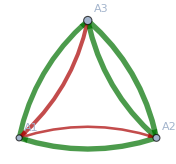

```mathematica
displayGraph[randomGameState[<|"n"->3,"α"-> 2.5,"ρ"->0.3,"maxInitSize"->1|>],False]
```

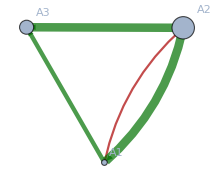

```mathematica
displayGraph[newState[{1.1,4.3,2.7}/3,{{0.7,0.1,0},{-0.1,0.8,0},{0.2,0.1,1}},<|"α"-> 2.5, "n"->3|>],False]
```

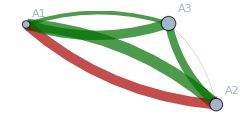

```mathematica
displayGraph[randomGameState[<|"n"->3,"α"-> 2.5,"ρ"->0.3,"maxInitSize"->1|>],False,{Entity["City",{"Coventry","Coventry","UnitedKingdom"}],Entity["City",{"Sarajevo","FederacijaBosnaIHercegovina","BosniaHerzegovina"}],Entity["City",{"Berlin","Berlin","Germany"}]}]
```

#### Display frame sequences

Display a sequence of game states:

```mathematica
displayFrameSequence[frameSequence_,showMetadataQ_] :=Map[Magnify[displayGraph[#,showMetadataQ],0.60]&,frameSequence]
```

Display a list of sequences of game states:

```mathematica
displayFrameSequences[frameSequenceData_, showMetadataQ_]:=Map[displayFrameSequence[#,showMetadataQ]&,frameSequenceData]
```

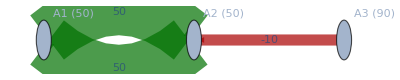
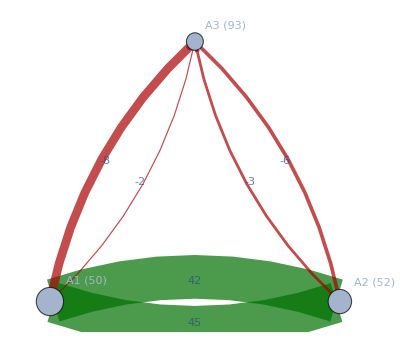
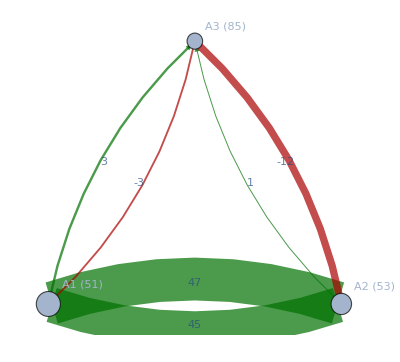
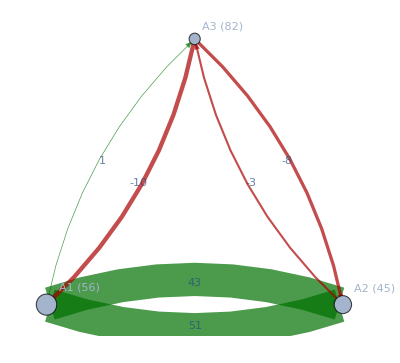
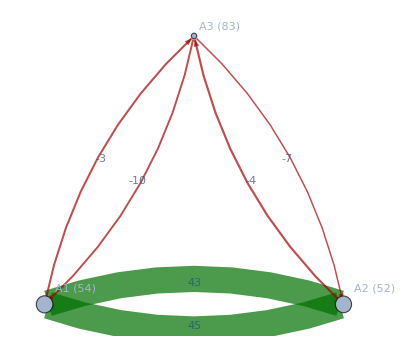
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
runAndShowFrameSequence[state,<|"n"-> 3,"α"-> 2.5, "β"-> 1.1, "μ"-> 3, "δ"-> 0.9, "σ"-> 6,"breadth"-> 13,"depth"->5,"nearness" -> 0.05|>,True]
```

#### Tactic plot

```mathematica
randomMatrixNear[IdentityMatrix[5],0.01]
```

{{0.985185,-0.00261689,0.000945784,0.00312958,0.00797882},{0.00415987,0.97963,0.00144437,0.00261578,-0.0122513},{0.00769785,0.0120576,0.985867,-0.0246635,0.0000536922},{0.00288223,-0.00476852,-0.00683518,0.956394,0.00819866},{-0.0000745872,-0.000927315,-0.00490801,-0.0131975,0.971517}}

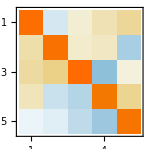

```mathematica
MatrixPlot[%280]
```

## Experimentation

### Tests

#### Parameter Explorer

A widget for exploring parameter space for a simple scenario.  Moving the “redo” slider generates a new simulation without altering any of the other variables.

```mathematica
Manipulate[runAndShowFrameSequence[
newState[{1,1,1},{{0.8,0.2,0},{0.2,0.8,-0.1},{0,0,0.9}},<|"α"-> α,"n"->3|>],
<|"n"-> 3,"α"-> α, "β"-> β, "μ"-> μ, "δ"-> δ, "σ"-> σ,"breadth"-> breadth,"depth"->depth,"nearness" -> nearness,"x"-> redo|>,False] // Column,{{α,2.5},2,3},{{β,1.1},1,10},{{μ,3},1,10},{{δ,0.8},0.001,1},{{σ,0.01},0.001,4},{{breadth,15},1,25,1},{{depth,5},1,15,1},{{nearness,0.05},0.001,1},{redo,0,1}]
```

#### WWI

Very preliminary: Europe (subset), August 1914.

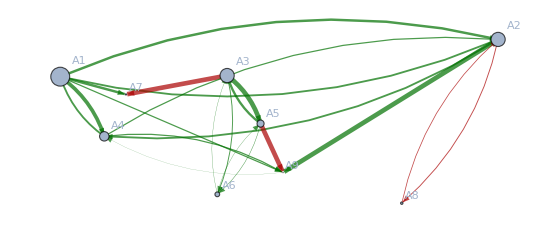

```mathematica
wwiCities = {Entity["City",{"Coventry","Coventry","UnitedKingdom"}],Entity["City",{"Moscow","Moscow","Russia"}],Entity["City",{"Berlin","Berlin","Germany"}],Entity["City",{"Bourges","Centre","France"}],Entity["City",{"Vienna","Vienna","Austria"}],Entity["City",{"Rome","Lazio","Italy"}],Entity["City",{"Brussels","Brussels","Belgium"}],Entity["City",{"Istanbul","Istanbul","Turkey"}],Entity["City",{"Sarajevo","FederacijaBosnaIHercegovina","BosniaHerzegovina"}]};wwiSizes = {0.8,0.6,0.6,0.4,0.3,0.2,0.05,0.1,0.02};
wwiTactics = {
{0.94,0.02,0,0.03,0,0,0,0,0},
{0.02,0.94,0,0.02,0,0,0,-0.05,0},
{0,0,0.90,0,0.05,0.01,0,0,0},
{0.03,0.02,0,0.98,0,0,0,0,0.05},
{0,0,0.05,0,0.94,0.01,0,0,0},
{0,0,0.01,0,0.01,1,0,0,0},
{0.02,0,-0.05,0,0,0,1,0,0},
{0,-0.01,0,0,0,0,0,0.95,0},
{0.01,0.05,0,0.02,-0.1,0,0,0,0.95}} ;
wwi = newState[wwiSizes,wwiTactics,<|"α"-> 2.5,"n"->3|>];
displayGraph[wwi,False,wwiCities]
```

```mathematica
wwiTactics// MatrixForm
```

(0.94 | 0.02 | 0 | 0.03 | 0 | 0 | 0 | 0 | 0
0.02 | 0.94 | 0 | 0.02 | 0 | 0 | 0 | -0.05 | 0
0 | 0 | 0.9 | 0 | 0.05 | 0.01 | 0 | 0 | 0
0.03 | 0.02 | 0 | 0.98 | 0 | 0 | 0 | 0 | 0.05
0 | 0 | 0.05 | 0 | 0.94 | 0.01 | 0 | 0 | 0
0 | 0 | 0.01 | 0 | 0.01 | 1 | 0 | 0 | 0
0.02 | 0 | -0.05 | 0 | 0 | 0 | 1 | 0 | 0
0 | -0.01 | 0 | 0 | 0 | 0 | 0 | 0.95 | 0
0.01 | 0.05 | 0 | 0.02 | -0.1 | 0 | 0 | 0 | 0.95)